```mathematica
L=Table[{RandomReal[]*2,Prime[x]},{x,20}];f[x_,y_]:=10x+Sin[y];l=Table[{L[[i,1]],L[[i,2]],f[L[[i,1]],L[[i,2]]]},{i,Length[L]}];
```

```mathematica
model= Exp[-((-Log[x])^b+(-Log[y])^b)^(1/b)]/.b->a
```

ⅇ^(-((-Log[x])^a+(-Log[y])^a)^(1/a))

```mathematica
u=0.00001;
```

```mathematica
ListPointPlot3D[c]
```

-Graphics3D-

```mathematica
fi=FindFit[c,model,{a},{x,y}]
```

{a→0.932511}

```mathematica
Show[ListPlot3D[g],Plot3D[model/.fi,{x,0,1},{y,0,1}]]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[g,PlotStyle->Directive[PointSize[Medium],Red]],Plot3D[model/.fi,{x,0,1},{y,0,1}]]
```

-Graphics3D-

```mathematica
ListPlot3D[{#[[1]],#[[2]],#[[3]]-model/.fi/.x->#[[1]]/.y->#[[2]]}&/@g,InterpolationOrder->50]
```

-Graphics3D-

```mathematica
{#[[1]],#[[2]],#[[3]]-model/.fi/.x->#[[1]]/.y->#[[2]]}&/@c
```

ListPlot3D[{0.38612,0.276796,0.339139,0.58822,0.0732842,0.107194,0.360956,0.431692,0.101936,0.311469,0.0126242,0.100838,0.571699,0.0549775,0.0575832,0.16761,0.255773,0.384971,0.518501,0.460148,0.05362,0.557474,0.0104573,0.459694,0.306298,0.414205,0.219628,0.290776,0.145678,0.584657,0.0769081,0.101937,0.378329,0.178432,0.245511,0.0902623,0.589878,0.0478866,0.276158,0.0611864,0.0156485,0.270761,0.0790041,0.0693993,0.720323,0.18514,0.110748,0.477882,0.226719,0.0944798,0.0384576,0.340488,0.144311,0.0751811,0.212142,0.163234,0.0648467,0.483244,0.657144,0.0610038,0.117031,0.0153923,0.14078,0.0140581,0.564859,0.175006,0.323312,0.282334,0.0420584,0.578986,0.030446,0.0969057,0.0788814,0.123994,0.268805,0.624703,0.28009,0.125063,0.222925,0.347652,0.202346,0.0414904,0.501146,0.0286505,0.129602,0.0146292,0.29926,0.117237,0.0211574,0.131065,0.00912669,0.00656747,0.359925,7.68491×10^-6,0.560954,0.00333676,0.0289626,0.186436,4.03143×10^-7,0.237025,0.348491,0.239742,0.0130885,0.822027,0.559685,0.0491425,0.119537,0.0388942,0.0239928,0.00636056,0.757082,0.0738748,0.0513837,0.170153,0.671082,0.121733,0.0495847,0.369402,0.104954,3.05882×10^-11,9.99972×10^-6,9.99972×10^-6,0.999979}]

{0.38612,0.276796,0.339139,0.58822,0.0732842,0.107194,0.360956,0.431692,0.101936,0.311469,0.0126242,0.100838,0.571699,0.0549775,0.0575832,0.16761,0.255773,0.384971,0.518501,0.460148,0.05362,0.557474,0.0104573,0.459694,0.306298,0.414205,0.219628,0.290776,0.145678,0.584657,0.0769081,0.101937,0.378329,0.178432,0.245511,0.0902623,0.589878,0.0478866,0.276158,0.0611864,0.0156485,0.270761,0.0790041,0.0693993,0.720323,0.18514,0.110748,0.477882,0.226719,0.0944798,0.0384576,0.340488,0.144311,0.0751811,0.212142,0.163234,0.0648467,0.483244,0.657144,0.0610038,0.117031,0.0153923,0.14078,0.0140581,0.564859,0.175006,0.323312,0.282334,0.0420584,0.578986,0.030446,0.0969057,0.0788814,0.123994,0.268805,0.624703,0.28009,0.125063,0.222925,0.347652,0.202346,0.0414904,0.501146,0.0286505,0.129602,0.0146292,0.29926,0.117237,0.0211574,0.131065,0.00912669,0.00656747,0.359925,7.68491×10^-6,0.560954,0.00333676,0.0289626,0.186436,4.03143×10^-7,0.237025,0.348491,0.239742,0.0130885,0.822027,0.559685,0.0491425,0.119537,0.0388942,0.0239928,0.00636056,0.757082,0.0738748,0.0513837,0.170153,0.671082,0.121733,0.0495847,0.369402,0.104954,3.05882×10^-11,9.99972×10^-6,9.99972×10^-6,0.999979}

```mathematica
ListÜ
```

Show[-Graphics3D-,Plot[model/.%,{x,0,2},{y,0,80}]]

-Graphics3D-

```mathematica
c={{0.754237,0.533898,0.386555},{0.338983,0.847458,0.252101},{0.983051,0.347458,0.352941},{0.90678,0.661017,0.596639},{0.194915,0.423729,0.07563},{0.516949,0.228814,0.109244},{0.5,0.754237,0.352941},{0.872881,0.508475,0.436975},{0.652542,0.169492,0.084034},{0.449153,0.728814,0.310924},{0.076271,0.20339,0.02521},{0.788136,0.135593,0.084034},{0.79661,0.737288,0.554622},{0.70339,0.084746,0.042017},{0.161017,0.40678,0.067227},{0.610169,0.29661,0.159664},{0.271186,0.957627,0.260504},{0.389831,0.991525,0.386555},{0.542373,0.966102,0.521008},{0.847458,0.559322,0.462185},{0.101695,0.584746,0.058824},{0.711864,0.805085,0.563025},{0.118644,0.110169,0.016807},{0.949153,0.491525,0.470588},{0.627119,0.516949,0.310924},{0.923729,0.457627,0.428571},{0.644068,0.364407,0.226891},{0.322034,0.923729,0.294118},{0.661017,0.237288,0.142857},{0.737288,0.813559,0.579832},{0.177966,0.483051,0.084034},{0.262712,0.432203,0.10084},{0.584746,0.677966,0.386555},{0.432203,0.449153,0.176471},{0.669492,0.389831,0.260504},{0.211864,0.474576,0.10084},{0.720339,0.838983,0.588235},{0.144068,0.381356,0.058824},{0.533898,0.550847,0.285714},{0.084746,0.771186,0.07563},{0.364407,0.050847,0.008403},{0.313559,0.889831,0.268908},{0.881356,0.09322,0.07563},{0.483051,0.161017,0.067227},{1.-u,0.720339,0.722689},{0.618644,0.322034,0.184874},{0.771186,0.152542,0.084034},{0.59322,0.830508,0.470588},{0.254237,0.915254,0.243697},{0.127119,0.788136,0.117647},{0.067797,0.627119,0.042017},{0.508475,0.70339,0.336134},{0.398305,0.398305,0.12605},{0.279661,0.305085,0.067227},{0.347458,0.652542,0.218487},{0.355932,0.5,0.159664},{0.110169,0.644068,0.07563},{0.838983,0.59322,0.478992},{0.966102,0.686441,0.663866},{0.372881,0.186441,0.042017},{0.491525,0.262712,0.109244},{0.025424,0.669492,0.02521},{0.169492,0.864407,0.151261},{0.050847,0.330508,0.02521},{0.728814,0.79661,0.563025},{0.559322,0.338983,0.176471},{0.567797,0.601695,0.319328},{0.677966,0.440678,0.310924},{0.40678,0.118644,0.042017},{0.762712,0.779661,0.563025},{0.457627,0.076271,0.033613},{0.305085,0.355932,0.084034},{0.135593,0.635593,0.084034},{0.474576,0.288136,0.117647},{0.288136,0.949153,0.268908},{0.745763,0.855932,0.621849},{0.415254,0.711864,0.277311},{0.440678,0.313559,0.117647},{0.576271,0.415254,0.218487},{0.525424,0.694915,0.344538},{0.855932,0.245763,0.210084},{0.228814,0.211864,0.042017},{0.694915,0.745763,0.512605},{0.330508,0.101695,0.016807},{0.152542,0.881356,0.151261},{0.016949,0.898305,0.02521},{0.550847,0.576271,0.294118},{0.237288,0.542373,0.134454},{0.09322,0.271186,0.033613},{0.779661,0.177966,0.109244},{0.423729,0.025424,0.008403},{0.042373,0.194915,0.016807},{0.974576,0.372881,0.369748},{0.830508,u,0.008403},{0.991525,0.567797,0.571429},{0.008475,0.466102,0.016807},{0.889831,0.033898,0.042017},{0.186441,1.-u,0.193277},{u,0.067797,0.008403},{0.245763,0.974576,0.243697},{0.381356,0.932203,0.352941},{0.957627,0.254237,0.260504},{0.822034,0.016949,0.016807},{0.915254,0.90678,0.823529},{0.932203,0.610169,0.563025},{0.20339,0.279661,0.05042},{0.864407,0.144068,0.117647},{0.940678,0.042373,0.05042},{0.033898,0.762712,0.033613},{0.805085,0.008475,0.008403},{0.813559,0.940678,0.756303},{0.635593,0.127119,0.067227},{0.898305,0.059322,0.058824},{0.29661,0.618644,0.168067},{0.686441,0.983051,0.672269},{0.601695,0.220339,0.109244},{0.059322,0.872881,0.058824},{0.466102,0.822034,0.352941},{0.220339,0.525424,0.117647},{u,u,u},{u,1-u,u},{1.-u,u,u},{1,1,1}(1-u)};
```

# Normal

```mathematica
PDF[NormalDistribution[a,b],x]
```

```mathematica
L=RandomReal[NormalDistribution[10,1],1000];
```

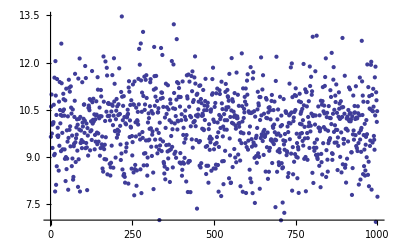

```mathematica
ListPlot[L]
```

```mathematica
n=Length[L];Ls=Sort[L];F=Table[{Ls[[i]],i/n},{i,1,n}];
```

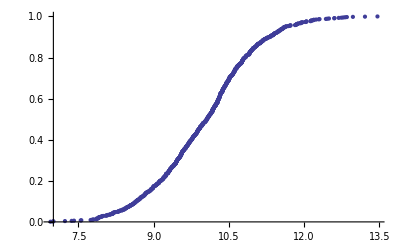

```mathematica
ListPlot[F]
```

```mathematica
fi=FindFit[F,CDF[NormalDistribution[a,b],x],{a,b},x]
```

{a→10.01,b→1.01656}

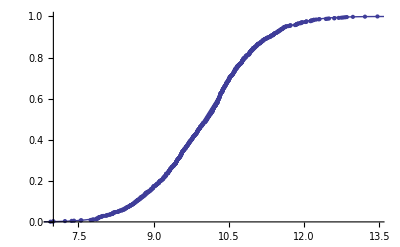

```mathematica
Show[ListPlot[F],Plot[CDF[NormalDistribution[a,b],x]/.fi,{x,6,14}]]
```

```mathematica
CDF[NormalDistribution[a,b],x]
```

1/2 (1+Erf[(-a+x)/(√2 b)])

# DAX

```mathematica
g={1443.2,1415.3,1420.6,1418.9,1441.2,1462.6,1446.3,1471.,1504.7,1512.8,1504.8,1492.7,1517.2,1517.8,1522.4,1475.9,1477.4,1457.2,1409.3,1414.9,1410.9,1398.2,1366.1,1366.7,1396.1,1358.2,1354.,1375.2,1383.4,1382.3,1327.8,1325.6,1322.7,1422.7,1405.1,1390.2,1375.1,1358.8,1375.2,1382.1,1382.7,1380.3,1400.7,1420.1,1426.5,1435.,1438.9,1428.7,1436.3,1467.8,1488.7,1468.9,1489.4,1486.5,1531.2,1572.6,1587.1,1567.3,1566.3,1582.5,1601.2,1558.2,1565.5,1542.1,1516.7,1530.9,1540.3,1594.3,1580.5,1580.5,1565.8,1571.6,1542.2,1576.6,1570.6,1552.9,1546.5,1517.9,1519.6,1520.3,1515.5,1498.4,1508.8,1522.8,1538.6,1577.5,1572.,1586.9,1580.,1582.1,1561.9,1565.4,1583.1,1601.4,1603.4,1623.8,1613.8,1599.4,1571.9,1597.1,1603.7,1620.5,1623.8,1620.3,1605.8,1630.,1631.8,1624.,1627.5,1607.3,1620.6,1610.9,1598.5,1590.4,1598.1,1598.9,1617.4,1647.7,1652.7,1671.9,1681.5,1682.1,1681.5,1704.1,1694.1,1685.4,1712.8,1704.2,1709.6,1704.9,1715.2,1700.8,1692.6,1699.8,1701.1,1695.4,1683.,1687.,1711.9,1691.6,1691.5,1672.1,1666.1,1622.2,1625.2,1610.5,1614.4,1616.1,1618.9,1605.,1627.6,1634.7,1637.9,1644.8,1646.6,1643.9,1625.5,1618.3,1624.,1623.,1632.9,1621.7,1615.4,1605.6,1605.6,1614.9,1622.3,1622.6,1615.4,1622.,1611.9,1631.4,1630.2,1632.2,1626.1,1644.7,1650.2,1654.3,1653.3,1497.9,1526.9,1570.8,1630.8,1627.2,1654.2,1647.1,1647.5,1655.5,1650.5,1650.5,1655.6,1647.9,1647.2,1646.2,1633.1,1629.1,1628.2,1631.3,1637.6,1629.8,1634.6,1628.1,1620.7,1616.1,1614.2,1626.6,1625.4,1620.,1608.1,1607.,1609.6,1607.3,1601.7,1588.7,1578.7,1567.2,1568.,1568.4,1571.,1585.,1570.1,1564.5,1563.3,1572.7,1580.7,1587.9,1579.,1572.,1576.8,1590.8,1582.8,1582.1,1573.6,1573.6,1576.1,1574.2,1578.4,1606.2,1609.,1621.2,1623.2,1621.,1629.4,1611.9,1599.1,1598.1,1600.3,1589.2,1602.9,1586.2,1588.2,1566.6,1545.4,1546.8,1561.,1553.4,1558.2,1559.1,1551.1,1543.6,1546.4,1558.3,1552.9,1560.9,1573.8,1561.8,1543.2,1539.6,1563.6,1578.,1601.9,1603.6,1603.3,1592.5,1578.7,1589.8,1615.7,1622.7,1628.5,1667.5,1666.3,1671.,1677.2,1685.3,1680.1,1669.6,1664.8,1683.6,1683.1,1672.4,1680.9,1687.5,1689.,1674.6,1686.6,1681.1,1685.5,1682.1,1683.6,1678.9,1681.4,1676.5,1681.1,1695.,1687.8,1703.2,1717.6,1729.1,1722.3,1737.3,1749.9,1745.1,1747.9,1763.3,1759.1,1764.8,1746.,1750.3,1750.5,1743.4,1727.5,1732.6,1724.8,1730.1,1732.2,1724.6,1736.3,1717.5,1713.1,1716.3,1719.,1711.5,1710.3,1717.9,1707.3,1721.7,1719.6,1734.6,1739.4,1720.,1720.3,1736.1,1727.7,1732.5,1743.8,1749.2,1746.5,1753.3,1752.4,1745.7,1742.2,1735.9,1735.9,1734.,1728.3,1732.6,1743.5,1750.8,1748.2,1753.,1751.2,1749.4,1742.3,1724.1,1758.4,1763.3,1787.5,1785.5,1803.,1811.6,1806.7,1794.1,1803.2,1798.1,1801.4,1788.6,1792.3,1789.1,1786.3,1789.8,1781.8,1782.3,1773.9,1779.1,1771.8,1772.9,1770.6,1771.1,1768.5,1764.9,1754.1,1757.1,1752.6,1756.3,1768.6,1777.,1772.4,1767.5,1751.2,1757.6,1754.5,1736.5,1734.1,1734.6,1740.5,1702.7,1649.7,1659.8,1628.2,1623.4,1610.4,1618.1,1610.6,1628.2,1624.,1615.4,1594.7,1611.5,1628.8,1621.2,1609.5,1582.6,1564.6,1553.,1541.,1547.8,1555.4,1533.2,1524.7,1513.1,1520.,1498.7,1468.9,1473.3,1513.4,1516.5,1541.3,1518.7,1506.7,1530.8,1536.5,1540.6,1544.6,1525.3,1528.3,1527.8,1595.,1587.6,1584.6,1578.7,1589.3,1573.9,1550.3,1557.8,1530.9,1513.4,1475.,1476.3,1466.4,1484.,1478.,1424.4,1420.3,1436.1,1451.1,1439.7,1432.5,1465.5,1458.5,1453.4,1461.6,1479.1,1511.6,1503.9,1510.1,1526.8,1542.5,1533.8,1510.3,1493.6,1492.3,1472.6,1485.,1472.7,1480.9,1487.2,1508.8,1519.1,1512.2,1535.4,1548.5,1547.,1545.1,1551.7,1544.8,1530.9,1510.3,1517.7,1523.2,1523.,1544.3,1544.9,1534.,1532.5,1522.2,1525.3,1508.2,1500.6,1494.5,1476.,1469.8,1481.2,1472.1,1476.2,1492.,1515.6,1523.6,1527.,1544.6,1542.2,1545.1,1531.3,1556.4,1556.4,1542.5,1531.5,1532.,1530.2,1516.5,1523.7,1544.6,1573.1,1578.8,1574.9,1573.7,1587.6,1569.2,1576.2,1562.3,1567.8,1571.9,1585.2,1583.1,1601.5,1601.6,1641.4,1647.2,1641.6,1649.8,1651.1,1661.4,1664.7,1664.2,1653.3,1672.3,1677.4,1680.7,1661.6,1644.2,1658.9,1684.4,1701.,1696.7,1693.7,1687.4,1682.8,1694.8,1713.1,1709.7,1717.4,1707.1,1702.6,1697.8,1685.1,1696.2,1698.8,1661.4,1648.4,1659.5,1657.2,1661.3,1674.9,1685.1,1684.2,1671.5,1661.8,1658.7,1665.4,1650.3,1655.7,1671.1,1672.4,1675.2,1678.9,1693.3,1687.1,1666.9,1666.7,1657.1,1649.8,1640.8,1628.9,1623.9,1627.2,1629.2,1627.4,1623.2,1623.3,1611.9,1609.,1616.2,1629.5,1639.8,1634.5,1627.9,1628.5,1617.4,1610.6,1603.1,1618.2,1622.,1634.5,1631.9,1619.9,1625.2,1629.6,1637.9,1655.6,1661.6,1673.1,1681.,1692.,1684.1,1689.6,1692.3,1686.9,1689.8,1698.1,1699.4,1686.3,1695.2,1707.2,1708.3,1697.6,1706.6,1697.8,1692.2,1700.9,1719.8,1783.7,1797.4,1818.2,1807.2,1811.6,1807.7,1813.5,1836.3,1839.,1823.8,1823.5,1830.8,1854.5,1845.2,1833.9,1833.7,1803.2,1815.1,1843.4,1860.6,1860.7,1869.4,1872.3,1865.2,1865.8,1905.,1906.6,1912.2,1910.2,1935.7,1939.,1922.7,1888.3,1897.7,1917.8,1901.2,1904.6,1921.9,1944.9,1918.6,1925.6,1925.2,1910.3,1886.,1885.3,1880.8,1861.4,1872.6,1880.6,1860.4,1855.7,1882.,1912.8,1925.9,1893.,1916.5,1885.9,1912.2,1913.6,1907.7,1915.7,1912.1,1923.7,1972.7,1987.1,1997.,2005.,2011.,1998.6,2001.5,1990.1,2015.,2033.3,2026.8,2042.6,2034.7,2066.2,2074.4,2058.7,2043.1,2038.5,2069.,2062.1,2095.6,2084.4,2062.6,2012.6,2010.8,2022.8,2023.8,2023.3,2015.,2049.1,2071.7,2085.3,2077.4,2030.,2027.4,2029.6,2047.7,2047.2,2043.4,2057.8,2089.9,2110.5,2120.6,2118.8,2115.5,2148.1,2175.8,2161.1,2172.8,2150.,2110.7,2137.5,2151.,2178.2,2182.9,2197.5,2222.8,2254.,2242.8,2214.7,2266.7,2268.,2253.6,2233.4,2220.2,2211.6,2233.8,2228.8,2209.2,2164.7,2141.8,2137.4,2113.8,2134.4,2116.2,2075.6,2080.,2126.8,2119.2,2125.1,2133.5,2177.5,2179.7,2184.,2151.7,2138.3,2079.4,2107.2,2085.3,2119.,2090.6,2116.,2115.6,2136.6,2128.7,2152.,2119.5,2107.6,2127.7,2090.3,2075.,2091.6,2067.1,2020.3,2038.,2060.1,2109.,2124.,2115.1,2141.1,2103.5,2145.2,2165.6,2172.7,2175.1,2155.6,2131.3,2141.3,2161.1,2161.7,2130.1,2161.4,2168.4,2147.5,2133.1,2158.3,2191.2,2201.4,2203.4,2225.3,2210.6,2209.2,2198.7,2200.4,2228.8,2172.4,2182.6,2197.,2213.9,2202.2,2243.2,2253.6,2251.2,2246.,2268.7,2252.3,2249.,2235.8,2237.,2218.9,2235.2,2243.6,2258.8,2271.1,2259.7,2267.4,2247.8,2249.7,2198.7,2158.8,2130.3,2141.,2118.2,2127.7,2129.7,2148.4,2163.1,2135.1,2145.2,2129.3,2133.1,2105.8,2074.7,2074.7,2054.9,2050.7,1968.8,1983.3,1994.4,2022.1,2005.3,1988.6,2018.3,2046.3,2025.3,2036.5,2054.4,2032.7,2035.7,2043.9,2050.9,2065.7,2048.1,2054.,2055.6,2093.6,2098.2,2128.8,2138.7,2113.3,2150.3,2136.2,2152.,2140.4,2122.8,2146.6,2153.8,2186.4,2198.9,2183.4,2184.8,2184.7,2164.2,2160.4,2155.3,2124.7,2138.8,2143.1,2162.3,2153.6,2149.6,2123.8,2107.9,2126.4,2152.2,2161.5,2193.2,2210.9,2212.9,2200.8,2204.7,2174.5,2165.9,2163.8,2172.4,2185.2,2154.6,2136.1,2124.1,2114.,2118.7,2096.8,2079.,2079.5,2073.,2089.1,2068.7,2058.7,2068.1,2043.6,2011.8,1995.,1968.7,1961.,1960.6,2024.8,2071.1,2077.6,2082.6,2105.7,2090.9,2084.8,2051.2,2070.,2022.2,2025.4,1974.6,2020.5,2013.2,2040.3,2071.6,2069.7,2042.4,2051.5,2067.6,2043.5,2053.4,2096.5,2082.4,2078.4,2089.3,2110.8,2102.7,2100.2,2105.3,2074.8,2033.3,2056.,2051.6,2058.5,2044.3,2048.3,2046.6,2038.5,2071.1,2046.9,2055.6,2042.2,2028.3,2024.8,2011.3,2024.8,2052.6,2070.1,2075.9,2079.9,2086.7,2100.7,2094.,2106.2,2109.,2077.,2106.6,2079.5,2074.8,2072.3,2062.5,2053.9,2059.2,2051.1,2061.1,2071.3,2055.6,2085.6,2083.9,2078.9,2089.4,2055.6,2026.8,2018.,2026.8,2030.7,2031.7,2035.,2021.3,2048.4,2045.3,2058.,2089.7,2092.5,2087.6,2112.7,2130.2,2117.,2133.2,2135.,2115.7,2117.,2101.5,2097.,2093.2,2118.2,2118.6,2099.3,2102.2,2126.2,2118.7,2109.5,2070.3,2053.3,2025.2,2001.6,1994.,1999.5,2000.5,2010.1,1992.1,2005.2,1991.8,1983.,1984.1,1936.1,1925.4,1946.9,1911.,1918.9,1918.5,1922.6,1930.8,1965.,1969.8,1979.3,1981.9,1972.3,1993.7,1988.5,1986.5,1965.3,1951.,1956.,1976.6,1976.2,2007.,2029.5,2026.1,2015.9,2035.9,2028.7,2044.8,2023.8,2024.8,2039.6,2059.1,2078.1,2096.9,2086.7,2110.5,2095.3,2087.1,2065.1,2083.2,2080.4,2105.1,2077.9,2067.4,2087.7,2092.2,2126.4,2136.3,2146.4,2141.1,2131.,2121.8,2119.6,2115.1,2128.,2120.,2141.8,2136.7,2143.7,2148.7,2139.8,2130.4,2122.4,2096.4,2106.6,2083.9,2092.3,2114.9,2105.7,2121.2,2153.4,2179.3,2201.9,2199.1,2214.4,2184.9,2199.6,2193.,2182.9,2184.3,2201.9,2197.5,2229.1,2240.8,2234.4,2230.,2218.7,2220.,2241.5,2240.7,2236.,2243.4,2237.7,2221.8,2218.7,2232.9,2208.5,2227.6,2252.9,2260.3,2263.5,2269.4,2258.9,2263.4,2262.9,2249.3,2241.1,2231.6,2240.1,2238.3,2233.1,2250.3,2264.8,2277.1,2268.,2273.7,2260.8,2270.8,2295.5,2300.,2317.,2301.4,2311.3,2305.1,2287.3,2211.8,2208.4,2227.9,2185.4,2171.9,2187.,2205.,2217.8,2208.8,2171.4,2168.7,2138.8,2145.3,2158.1,2196.8,2191.4,2201.,2194.8,2179.6,2170.5,2107.4,2113.6,2150.1,2131.8,2096.1,2146.1,2167.9,2163.2,2184.,2181.7,2165.8,2175.,2172.3,2192.8,2172.2,2175.3,2197.3,2186.2,2200.7,2201.3,2218.3,2205.1,2193.3,2192.3,2198.2,2238.1,2241.5,2245.6,2242.8,2260.7,2252.2,2261.,2267.2,2263.1,2267.5,2272.8,2289.8,2277.8,2285.9,2284.8,2266.2,2235.6,2262.1,2265.1,2280.4,2280.4,2275.8,2253.9,2284.9,2329.2,2324.3,2331.9,2323.5,2349.7,2338.2,2329.5,2356.5,2359.1,2376.9,2371.3,2380.9,2398.8,2390.5,2384.5,2423.1,2443.7,2432.9,2446.1,2435.8,2470.1,2459.3,2452.1,2419.,2428.3,2446.2,2430.2,2411.9,2428.1,2433.9,2427.1,2423.,2429.,2398.6,2382.6,2391.1,2412.,2451.8,2442.3,2444.9,2472.5,2473.6,2501.2,2488.,2479.,2466.,2480.9,2469.1,2407.8,2436.,2426.4,2426.5,2458.2,2463.2,2493.3,2485.9,2504.1,2504.2,2510.3,2499.3,2525.4,2508.4,2485.9,2489.1,2501.2,2494.4,2495.2,2503.3,2530.,2509.7,2511.8,2545.9,2538.4,2524.2,2535.5,2536.5,2545.9,2550.2,2538.3,2532.4,2537.2,2506.5,2505.3,2502.3,2457.5,2468.9,2479.5,2472.6,2469.4,2468.8,2496.2,2519.7,2528.8,2537.3,2550.,2570.8,2556.9,2560.5,2542.2,2558.3,2551.5,2527.3,2542.8,2532.8,2546.3,2552.5,2557.4,2558.8,2546.4,2568.9,2567.5,2548.8,2546.1,2549.3,2554.3,2539.7,2540.1,2566.4,2573.,2573.7,2551.6,2561.4,2564.,2572.3,2569.,2577.4,2583.5,2551.,2562.2,2567.4,2575.5,2544.3,2550.5,2469.8,2497.2,2506.2,2520.2,2482.4,2475.1,2447.8,2465.,2470.3,2477.8,2457.5,2473.4,2494.5,2508.7,2520.9,2522.5,2531.9,2538.2,2525.6,2528.2,2539.4,2538.7,2546.3,2548.4,2562.8,2560.3,2543.7,2557.3,2555.2,2552.4,2558.8,2563.2,2560.1,2543.8,2532.9,2510.8,2532.4,2529.5,2517.,2548.7,2570.1,2566.8,2570.3,2596.,2629.9,2628.1,2625.7,2624.4,2646.1,2627.,2638.5,2659.,2666.6,2659.,2651.9,2655.7,2676.5,2683.3,2702.6,2691.2,2703.,2680.8,2686.,2693.9,2728.5,2714.9,2716.3,2734.8,2729.,2719.,2699.5,2678.4,2674.2,2703.8,2673.6,2678.7,2659.3,2683.3,2671.9,2691.3,2729.2,2713.2,2739.8,2728.3,2734.3,2773.4,2777.,2795.8,2763.8,2764.1,2774.5,2772.3,2763.7,2799.2,2810.6,2797.,2817.5,2845.5,2858.6,2887.,2866.1,2909.9,2792.,2857.2,2891.,2841.1,2847.1,2799.7,2855.8,2815.1,2820.8,2807.8,2854.5,2845.6,2852.9,2888.7,2848.8,2859.3,2881.3,2886.1,2906.3,2892.6,2933.4,2955.,2949.,2988.5,2993.3,3001.4,3030.7,2976.7,3028.7,3033.5,2998.2,2994.5,2989.3,2999.2,3017.3,3035.2,3062.3,3067.1,3098.,3104.1,3138.,3184.4,3187.6,3216.1,3229.5,3248.2,3232.6,3276.2,3233.8,3196.,3184.1,3184.2,3233.2,3237.9,3276.7,3259.6,3263.9,3320.7,3365.,3417.6,3376.2,3436.1,3460.6,3415.4,3349.8,3359.3,3351.,3291.2,3315.9,3264.7,3298.2,3321.8,3349.1,3418.1,3429.1,3295.9,3301.9,3215.2,3244.9,3312.9,3329.8,3359.5,3351.5,3340.1,3279.9,3327.7,3353.5,3383.3,3344.4,3347.6,3340.3,3396.,3397.4,3374.1,3363.1,3383.2,3438.1,3460.4,3528.8,3568.3,3552.,3562.4,3575.4,3595.2,3573.7,3562.1,3604.6,3543.4,3596.1,3579.4,3602.2,3657.9,3674.4,3636.4,3562.7,3596.4,3655.6,3651.6,3684.6,3700.5,3668.6,3671.2,3671.9,3737.2,3752.4,3750.,3721.2,3730.6,3777.6,3788.5,3748.8,3761.1,3819.5,3820.2,3809.9,3766.9,3834.8,3867.5,3939.7,3946.7,4003.4,4030.1,4027.,4000.7,4074.3,4142.2,4139.7,4223.7,4203.9,4131.9,4140.,4297.6,4384.8,4320.5,4368.5,4400.3,4377.7,4458.7,4405.5,4337.,4302.5,4325.9,4364.3,4428.1,4342.3,4333.2,4377.5,4237.1,4195.5,4077.6,4080.6,4190.5,4251.9,4204.8,4090.1,4076.8,3993.7,3992.,3897.4,3919.8,4001.8,4127.3,4062.1,4093.4,4073.7,4131.3,4104.6,4028.,3890.2,3796.6,3869.5,3995.7,3970.4,4004.,3983.1,4096.9,4091.8,4151.,4104.9,4135.1,4116.5,4154.9,4263.,4266.2,4326.4,4311.1,4267.4,4179.9,4164.6,4225.3,4215.2,4168.6,4149.9,4049.2,4069.3,4172.5,4124.9,3976.4,3981.4,3871.4,3645.7,3806.7,3748.9,3753.7,3847.7,3784.8,3841.4,3813.9,3715.4,3728.4,3734.8,3697.5,3701.9,3676.7,3816.7,3844.1,3876.9,3931.8,3941.9,3832.1,3850.1,3926.9,3962.,3972.1,4125.9,4096.4,4074.6,4159.7,4191.8,4208.1,4187.1,4117.27,4016.7,4061.9,4029.1,4150.3,4154.6,4162.9,4055.4,4125.5,4132.8,4266.,4224.3,4364.3,4417.,4360.1,4340.,4293.6,4237.8,4134.6,4150.1,4145.4,4140.2,4216.2,4290.1,4310.8,4250.5,4238.8,4222.2,4266.3,4316.1,4385.3,4444.5,4442.5,4529.9,4529.2,4509.3,4494.7,4536.9,4519.6,4558.6,4552.5,4509.4,4522.4,4535.6,4627.4,4611.7,4581.1,4583.,4610.7,4604.6,4704.6,4695.8,4693.9,4781.6,4759.6,4690.5,4676.4,4762.7,4828.9,4852.2,4862.4,4838.7,4872.2,4905.6,4945.9,4908.6,4949.9,5045.2,5014.1,5064.4,5114.1,5029.,5066.9,5069.9,5097.3,5135.4,5179.,5254.3,5345.9,5309.7,5267.4,5312.3,5368.,5359.2,5293.,5326.6,5407.9,5373.8,5312.3,5262.6,5144.4,5002.7,5018.67,5108.48,5107.44,5314.66,5232.03,5229.8,5186.23,5257.58,5341.69,5297.35,5376.88,5361.22,5393.14,5342.85,5388.9,5510.98,5564.21,5575.16,5644.29,5490.64,5481.26,5569.08,5582.78,5613.76,5592.48,5688.5,5779.09,5760.03,5754.46,5670.83,5527.32,5591.57,5709.36,5718.06,5702.61,5654.75,5718.71,5779.91,5866.63,5870.42,5915.13,5897.44,5906.85,5904.1,5953.16,5918.37,5960.98,6013.14,5996.77,5982.42,6019.48,6095.28,6108.24,6094.02,6147.87,6171.43,6165.52,6110.73,6058.45,6035.28,5885.,5889.01,5853.63,5880.87,5873.92,5758.77,5756.2,5632.51,5517.64,5581.22,5476.25,5268.4,5402.37,5356.23,5447.9,5456.58,5568.88,5596.41,5488.22,5163.51,5234.88,5372.76,5231.61,5060.84,4993.54,4833.89,4791.81,4970.5,4812.18,4820.25,4923.37,5103.84,5040.87,4747.33,4737.15,4896.49,4831.22,4857.97,4669.51,4598.58,4433.87,4575.15,4699.39,4646.25,4561.58,4653.94,4578.27,4474.51,4226.49,3962.5,4034.23,4156.64,4087.83,3896.08,3983.65,4225.49,4274.48,4318.52,4399.05,4489.1,4458.4,4595.82,4523.24,4454.28,4451.09,4577.74,4682.45,4536.34,4549.33,4671.12,4761.15,4705.08,4841.72,4811.6,4836.22,4768.58,4662.78,4717.7,4639.89,4639.65,4783.77,4702.63,4698.72,4795.69,4911.88,5019.12,4958.82,4944.37,5051.63,5121.48,5022.7,4781.73,4691.69,4787.08,4775.23,4713.96,4699.34,4663.68,4642.69,4536.2,4522.86,4574.5,4663.45,4723.81,4629.23,4780.93,4825.38,4951.77,5044.77,5031.87,5002.39,5252.36,5253.91,5443.62,5323.21,5392.84,5270.6,5200.1,4931.8,4912.75,4960.22,5050.4,5073.15,5143.06,5156.67,5019.28,4982.45,4986.8,5061.18,5096.41,5159.96,5190.82,5166.87,5085.66,5077.85,5080.77,5027.22,4904.35,4796.82,4839.33,4888.74,4879.55,4904.68,4810.09,4845.08,4802.38,4845.18,4987.56,5062.31,4958.58,4911.81,4784.31,4804.02,4697.67,4678.72,4839.09,4788.69,4758.46,4721.41,4754.41,5008.16,5029.24,5094.63,5077.43,5013.62,5099.48,5027.06,4915.03,4780.13,4860.26,4775.17,4876.92,4856.84,4884.2,4914.59,4965.29,5052.27,5068.75,5124.18,5159.16,5199.18,5182.16,5181.01,5155.35,5220.15,5087.29,5163.29,5218.82,5195.42,5256.22,5347.5,5348.61,5334.42,5393.11,5377.56,5383.21,5307.22,5274.45,5297.38,5205.95,5249.15,5248.02,5173.25,5114.47,5154.94,5184.51,5235.64,5264.68,5143.1,5160.44,5083.83,5068.73,5069.83,5021.24,4997.83,5107.81,5190.15,5211.08,5253.89,5206.47,5262.15,5268.87,5342.86,5381.25,5412.,5430.32,5468.47,5468.67,5399.11,5327.6,5301.21,5356.95,5359.53,5378.52,5480.22,5519.05,5625.62,5612.9,5588.5,5607.1,5638.95,5652.02,5573.82,5610.89,5619.26,5619.94,5624.74,5491.29,5414.17,5340.91,5310.63,5206.44,5224.16,5229.56,5052.32,5101.87,5129.5,5107.68,5119.37,4978.45,5010.47,5087.3,5000.87,5019.69,5127.43,5219.43,5257.1,5259.91,5230.47,5186.85,5254.14,5301.98,5324.02,5400.32,5389.34,5420.36,5392.53,5270.77,5317.12,5189.92,5336.22,5400.55,5391.36,5400.7,5436.86,5483.95,5446.91,5401.47,5387.18,5304.42,5303.94,5351.98,5282.76,5238.76,5299.57,5186.53,5239.64,5119.1,5135.62,5149.83,5124.55,5218.86,5301.85,5353.32,5419.31,5419.26,5414.5,5358.46,5295.43,5220.29,5184.23,5156.28,5296.91,5291.23,5246.49,5357.75,5320.4,5388.76,5363.86,5478.89,5525.4,5524.92,5546.95,5560.87,5635.62,5658.1,5647.94,5694.73,5742.42,5802.36,5791.05,5859.29,5909.52,5870.17,5950.05,5955.97,5819.89,5814.74,5818.73,5961.45,5958.07,5888.88,5896.04,5933.84,5937.2,6119.17,6142.19,6158.77,6115.59,6118.06,6097.9,6127.2,6187.99,6232.75,6341.29,6353.9,6378.66,6418.68,6492.53,6782.39,6837.41,6861.54,6859.58,6958.14,6750.76,6586.95,6502.07,6474.92,6780.96,6925.52,6891.25,6912.81,6955.98,7173.22,7258.9,7072.12,7091.04,7112.66,6992.75,6931.99,6809.64,6969.37,7126.13,7066.6,6835.6,7050.46,7171.95,7354.26,7444.61,7296.32,7549.88,7629.11,7709.27,7611.55,7644.8,7396.13,7490.32,7580.53,7573.78,7590.53,7607.94,7698.97,7640.53,7738.68,7587.13,7644.55,7727.93,7945.77,7960.03,7975.78,8064.97,7987.,7949.15,7975.95,7693.85,7650.05,7414.46,7583.96,7710.92,7872.38,7807.93,7798.62,7694.78,7932.42,7892.49,7931.93,7864.76,7644.89,7599.39,7429.22,7522.8,7330.77,7446.21,7522.2,7516.95,7442.66,7443.07,7449.06,7214.83,7187.14,7196.49,7216.71,7157.95,7280.51,7388.55,7221.74,7414.68,7555.92,7376.93,7386.71,7530.82,7408.09,7280.54,7120.86,7259.48,7269.28,7195.15,7371.06,7211.51,7181.58,6989.03,6912.96,6927.69,6834.88,6978.87,6839.33,7016.66,7119.26,7109.67,7272.76,7438.95,7408.02,7359.8,7285.93,7253.46,7246.79,7240.1,7268.91,7350.94,7328.62,7252.58,7198.8,7227.27,7100.09,7064.73,6980.41,7027.19,7048.96,7054.3,6881.94,6882.44,6962.02,6944.36,6961.73,6972.8,7044.77,7066.22,7006.05,7065.97,7166.51,7321.94,7430.7,7406.91,7366.57,7480.14,7378.86,7314.2,7329.46,7268.,7183.44,7128.3,7190.37,7145.53,7112.45,7011.74,7016.59,7113.22,7143.96,7226.71,7280.97,7322.98,7331.67,7307.43,7315.27,7278.43,7232.42,7199.34,7249.2,7232.78,7230.26,7307.17,7339.22,7294.4,7192.69,7244.79,7344.67,7445.56,7391.27,7329.9,7373.34,7261.04,7214.45,7135.75,7006.26,7049.82,6999.54,6891.69,6915.49,6765.23,6682.92,6740.25,6788.69,6765.04,6814.06,6832.76,6798.12,6862.26,6823.43,6892.49,6776.39,6680.78,6673.15,6554.14,6465.26,6661.3,6627.25,6531.71,6470.06,6619.43,6615.9,6620.87,6802.81,6748.22,6767.9,6924.68,6926.57,7077.44,7059.07,7088.64,7128.27,7136.3,7083.7,7010.2,6959.5,6851.69,6742.1,6966.65,6961.09,6811.49,6752.29,6605.53,6666.06,6510.54,6596.93,6664.18,6696.91,6625.56,6598.32,6372.33,6512.91,6408.1,6637.09,6622.25,6583.13,6691.25,6782.52,6733.59,6620.21,6475.84,6331.3,6390.25,6479.28,6248.76,6200.71,6251.4,6328.16,6371.64,6433.61,6289.82,6434.96,6376.54,6382.31,6392.17,6404.52,6320.07,6465.21,6490.03,6522.87,6502.89,6653.38,6635.76,6651.53,6675.,6722.41,6706.67,6727.49,6695.2,6750.96,6739.3,6795.14,6704.68,6638.2,6628.07,6693.03,6578.96,6636.81,6497.07,6564.91,6557.93,6479.87,6591.67,6439.26,6472.21,6451.57,6347.99,6277.99,6075.34,6189.07,6220.48,6208.24,6123.38,6159.02,6216.38,6284.06,6305.64,6267.06,6204.42,6046.56,5962.93,5794.12,5889.95,5734.49,5657.29,5782.16,5622.09,5388.02,5544.67,5726.97,5938.21,5817.52,5879.3,5829.95,5760.76,5553.46,5597.66,5773.34,5698.88,5781.01,5913.84,5951.16,6002.3,5935.58,6164.88,6181.91,6127.97,6051.48,6124.57,6115.19,6123.66,6175.24,6264.51,6213.84,6089.17,6138.28,6122.62,6108.72,6063.94,6165.18,6141.02,6064.68,6070.38,6148.44,6173.81,6186.87,6249.87,6270.59,6215.25,6278.9,6223.57,6216.83,6120.33,6041.22,6123.26,6125.17,6177.74,6242.13,6192.44,6184.25,6187.21,6162.74,6059.15,6111.94,6031.27,5915.18,5869.04,5922.53,5876.04,5926.38,5941.77,5902.32,5847.79,5833.1,5971.77,6058.38,6109.5,6056.84,6015.72,5999.19,5862.1,5869.86,5816.32,5801.8,5889.88,5928.01,5853.76,5846.66,5728.37,5829.69,5764.06,5791.73,5663.26,5582.76,5675.76,5754.86,5792.19,5861.19,5835.23,5777.28,5735.88,5746.04,5752.51,5614.51,5512.28,5433.49,5453.77,5520.71,5455.44,5361.92,5222.12,5207.83,5216.11,5220.21,5254.04,5387.5,5406.47,5308.78,5305.,5162.4,5188.17,5094.1,5208.1,5048.08,4875.37,4730.67,4670.13,4369.57,4392.4,4115.98,4243.68,4194.85,4041.8,3809.67,3787.23,4038.69,4009.12,4095.32,4184.5,4308.15,4239.97,4304.2,4436.66,4548.13,4487.69,4495.15,4472.42,4613.19,4718.46,4625.13,4548.48,4626.48,4644.82,4574.37,4513.53,4619.32,4704.22,4811.82,4715.6,4820.26,4660.35,4543.98,4559.13,4636.13,4583.31,4755.11,4707.65,4860.66,4993.57,4910.07,4820.37,4946.97,4953.53,5006.33,5062.64,5185.1,5096.18,5087.03,5124.54,5150.97,5114.12,5059.57,4915.95,4936.08,4989.91,4988.44,5013.99,5262.75,5271.29,5199.03,5124.68,5146.45,5062.56,4966.05,4909.42,5067.99,5039.64,4984.69,4934.14,5019.01,5117.13,5160.1,5167.88,5270.29,5318.73,5232.22,5236.37,5288.21,5228.11,5209.97,5065.84,5062.04,4984.2,5133.4,5122.23,5069.74,5045.72,5163.03,5170.44,5156.63,5159.02,5084.52,5052.2,5107.61,5097.06,4984.48,4936.75,4804.41,4862.62,4835.95,4940.,4884.78,4935.35,4973.77,4862.6,4871.76,4764.05,4780.24,4850.73,4745.58,4863.54,4897.75,4960.22,5039.08,5097.41,5245.84,5228.67,5285.26,5289.43,5359.55,5340.67,5275.81,5245.99,5276.87,5401.11,5426.04,5462.55,5364.7,5348.68,5366.13,5317.38,5390.59,5348.,5397.29,5311.08,5281.84,5254.95,5260.53,5180.33,5170.25,5265.36,5162.96,5189.65,5244.2,5343.88,5318.55,5262.88,5284.55,5205.48,5192.1,5160.14,5054.41,5000.38,5008.04,5041.2,4964.56,4882.77,4880.67,4872.41,5028.59,4966.48,4871.7,4975.48,5049.08,5072.39,5047.45,5036.41,4998.99,4984.61,4919.5,4879.5,4899.13,4961.54,4918.58,4881.8,4761.96,4818.3,4747.95,4625.79,4624.31,4657.52,4610.18,4589.26,4606.09,4510.19,4470.14,4303.85,4475.1,4433.85,4354.82,4245.68,4232.4,4127.21,4202.97,4099.05,4259.43,4382.56,4366.81,4195.95,4138.15,4258.62,4483.03,4442.33,4369.76,4190.22,4118.5,4130.8,3912.51,3977.75,4092.82,4100.75,3891.88,3691.43,3515.83,3632.66,3520.46,3579.,3859.78,3878.94,3700.14,3606.45,3532.49,3332.65,3568.64,3465.54,3679.26,3760.86,3647.13,3683.21,3589.92,3665.74,3684.69,3837.67,3768.51,3868.17,3906.55,3828.26,3783.84,3851.34,3682.84,3660.95,3712.94,3609.41,3398.99,3425.9,3354.71,3485.68,3429.22,3494.69,3584.69,3421.87,3361.28,3319.05,3289.13,3124.92,3007.47,3065.73,2914.25,2873.21,2962.5,3020.6,2918.9,2769.03,2865.23,2926.74,2813.3,2714.62,2667.39,2622.09,2597.88,2733.19,2930.74,2850.11,3048.27,3008.93,3172.46,3163.67,3282.67,3155.97,3015.42,3090.01,3102.01,3198.96,3022.01,3113.59,3152.85,3165.16,3327.94,3351.32,3298.84,3155.66,3079.1,3042.06,3115.88,3066.42,3188.39,3191.76,3218.36,3206.93,3212.99,3304.63,3320.88,3299.24,3191.63,3346.14,3360.76,3320.32,3380.2,3280.49,3320.75,3224.74,3207.53,3065.57,3167.99,3196.05,3111.88,3077.06,3205.29,3139.97,3022.69,2961.41,3024.22,3000.84,2840.,2892.63,3105.04,3092.94,3157.25,3112.77,2993.,3037.68,3037.33,3060.65,3098.72,3049.4,3054.11,2918.82,2893.55,2870.57,2803.25,2811.22,2717.82,2643.8,2671.36,2706.57,2693.78,2747.83,2751.99,2632.98,2725.88,2649.,2569.34,2586.09,2627.,2571.25,2555.27,2674.46,2708.97,2740.14,2624.65,2591.26,2648.87,2571.35,2485.5,2450.2,2513.22,2547.05,2549.65,2501.03,2498.02,2437.51,2431.66,2329.04,2305.3,2202.96,2354.31,2403.19,2487.12,2584.61,2615.22,2604.85,2715.06,2548.37,2636.1,2579.33,2584.05,2520.84,2423.87,2450.19,2589.35,2569.81,2654.07,2808.94,2767.79,2734.1,2697.1,2733.95,2776.78,2834.12,2824.68,2899.78,2960.96,2974.4,2891.62,2838.23,2953.92,2908.96,2942.04,2986.,3013.04,3066.95,3005.64,2886.08,2956.59,2937.26,2909.95,2926.03,2989.38,2989.08,2850.68,2838.93,2827.25,2865.21,2822.83,2828.28,2873.6,2919.54,2906.71,2982.68,3064.56,3026.82,3080.02,3039.76,3127.46,3094.76,3140.34,3178.15,3219.47,3168.71,3264.5,3286.48,3304.15,3247.11,3238.98,3186.39,3217.34,3198.82,3241.22,3224.66,3220.58,3146.55,3241.04,3241.92,3239.61,3332.87,3344.46,3322.43,3269.84,3326.51,3396.07,3384.69,3387.64,3330.68,3366.71,3287.,3318.15,3304.48,3374.82,3356.89,3417.77,3428.12,3429.03,3487.86,3438.89,3405.31,3438.36,3375.66,3331.89,3332.24,3339.58,3381.71,3398.89,3452.7,3443.93,3507.23,3504.53,3501.23,3565.47,3549.05,3500.09,3455.48,3483.08,3492.67,3484.58,3571.22,3567.2,3647.51,3668.67,3607.71,3641.53,3594.4,3536.87,3566.85,3508.06,3516.31,3564.75,3561.03,3612.02,3578.7,3456.27,3411.02,3307.34,3326.27,3324.85,3323.38,3256.78,3329.83,3276.64,3419.,3404.91,3355.78,3395.33,3481.9,3471.25,3538.39,3538.13,3570.58,3577.72,3516.67,3559.33,3580.08,3490.6,3497.14,3452.64,3517.1,3586.93,3615.42,3639.66,3655.99,3744.5,3741.71,3717.7,3733.93,3782.56,3746.24,3729.87,3748.34,3765.59,3797.4,3674.54,3666.28,3652.29,3638.04,3642.25,3737.09,3733.16,3712.98,3744.99,3745.95,3821.2,3809.26,3875.66,3874.78,3841.73,3806.54,3846.18,3820.92,3858.85,3860.13,3875.47,3865.98,3847.57,3870.88,3898.42,3876.94,3903.34,3952.72,3965.16,4018.5,4035.9,4035.44,4004.4,4045.43,4016.18,3995.91,3996.22,4055.21,4068.75,4111.64,4139.92,4106.41,4138.04,4139.86,4151.83,4128.68,4134.42,4150.24,4095.71,4058.6,4071.6,4057.51,4028.37,4014.79,4044.99,4098.97,4110.8,4122.16,4121.65,4057.05,4070.46,4095.86,4095.34,4141.53,4073.35,4068.71,3991.42,3995.34,4007.81,4018.16,4054.43,4100.34,4071.7,4133.78,4126.14,4145.99,4087.55,4044.7,3904.95,3915.38,3810.76,3822.37,3896.79,3827.43,3819.15,3729.23,3728.82,3726.07,3811.92,3822.33,3881.25,3874.04,3856.7,3924.85,4007.6,4048.6,4022.81,4001.16,4013.53,4071.42,4012.77,4004.61,4033.98,4025.07,4061.13,4026.15,4059.15,4103.62,4125.83,4134.1,4065.74,4008.91,3985.21,4007.65,3990.75,4022.1,3909.46,3895.64,3784.61,3849.84,3776.24,3824.93,3803.1,3754.37,3789.24,3872.26,3839.32,3831.84,3867.84,3828.07,3867.52,3913.33,3902.72,3921.41,3864.18,3888.31,3917.08,3961.93,4017.81,4018.95,3997.76,4021.64,4014.56,3948.65,3987.3,4003.24,3985.46,3999.79,3989.31,3928.39,3945.1,4007.05,4013.35,4069.35,4069.73,4052.73,4035.02,3998.77,3995.73,3944.88,3930.58,3934.48,3924.49,3893.24,3903.88,3898.84,3847.19,3845.93,3812.63,3837.6,3877.48,3801.05,3797.33,3752.59,3814.08,3807.21,3889.68,3895.61,3862.71,3877.32,3823.74,3829.03,3727.74,3690.33,3720.64,3678.91,3658.11,3646.99,3699.11,3705.73,3726.5,3722.99,3712.61,3772.14,3771.,3788.88,3832.28,3851.18,3838.85,3785.21,3817.62,3833.45,3866.99,3887.58,3889.04,3884.16,3851.22,3886.03,3953.31,3947.75,3941.75,3963.65,3988.07,3977.68,3991.02,3942.35,3905.66,3910.3,3874.37,3882.27,3920.36,3892.9,3994.96,4033.28,4048.71,4049.66,4043.36,4015.54,4017.82,3957.6,3976.03,3940.46,3922.11,3915.17,3964.13,3912.4,3934.06,3935.14,3854.41,3862.26,3929.03,3959.59,3960.25,4012.64,4037.57,4039.04,4041.38,4063.58,4068.97,4065.33,4089.13,4130.81,4143.35,4134.34,4117.22,4183.41,4178.68,4134.89,4123.98,4113.37,4125.3,4160.35,4154.27,4146.98,4126.,4186.03,4216.4,4208.87,4193.91,4212.62,4201.35,4150.41,4174.55,4219.24,4231.3,4213.69,4233.71,4182.27,4211.55,4214.39,4241.28,4251.62,4235.36,4261.79,4247.75,4256.08,4291.53,4290.5,4258.24,4300.94,4316.4,4307.37,4258.01,4208.82,4212.14,4232.36,4245.51,4250.71,4245.55,4220.43,4213.7,4201.89,4233.95,4214.12,4216.41,4201.81,4254.85,4279.97,4296.31,4281.64,4339.28,4366.35,4371.39,4353.15,4342.01,4387.8,4386.4,4402.03,4368.77,4369.68,4359.47,4353.34,4323.21,4310.66,4304.29,4348.64,4350.49,4383.62,4393.43,4373.27,4423.52,4428.09,4396.5,4375.6,4337.68,4360.49,4367.3,4387.69,4309.11,4315.92,4327.18,4296.36,4320.69,4317.2,4343.6,4351.89,4347.52,4348.77,4373.53,4341.39,4362.61,4379.18,4389.52,4400.68,4396.09,4372.12,4405.69,4402.05,4312.25,4202.2,4204.61,4178.62,4193.7,4223.04,4246.96,4233.76,4189.02,4178.1,4184.84,4224.02,4245.54,4264.35,4299.51,4311.06,4292.41,4251.13,4244.16,4267.05,4275.7,4262.18,4251.77,4324.6,4360.42,4360.68,4406.95,4396.64,4389.54,4436.6,4444.71,4480.43,4460.63,4527.17,4532.17,4510.39,4497.26,4566.01,4557.29,4562.75,4586.1,4599.21,4591.69,4548.42,4579.87,4604.57,4586.86,4608.11,4619.6,4627.48,4566.48,4523.82,4557.46,4583.63,4586.28,4617.07,4623.41,4603.65,4615.49,4530.18,4597.97,4663.38,4653.03,4679.89,4699.27,4712.9,4719.57,4770.54,4784.5,4829.87,4836.9,4842.7,4843.49,4855.35,4892.5,4886.5,4890.85,4932.87,4923.12,4874.06,4827.18,4837.86,4909.48,4990.57,4953.93,4937.33,4922.34,4883.81,4871.46,4851.27,4929.91,4941.69,4917.74,4915.95,4856.01,4783.8,4812.24,4791.72,4829.69,4842.94,4837.81,4909.89,4968.28,4988.14,4992.75,5005.93,4989.98,4901.88,4911.17,4905.98,4986.5,4926.13,4962.86,4875.22,4849.01,4882.58,4998.16,4965.88,5048.74,5021.17,5044.12,5082.07,5138.02,5069.42,5017.27,5007.77,5022.79,5032.46,4981.77,4950.07,4975.56,4978.83,4947.18,4845.98,4864.25,4838.4,4901.79,4872.97,4900.79,4806.05,4825.64,4929.07,4922.55,4954.83,5011.,4995.24,5024.2,5008.83,5011.38,5015.55,5090.75,5092.43,5110.61,5081.46,5099.72,5123.5,5170.61,5174.72,5196.08,5187.98,5194.27,5176.59,5199.48,5193.4,5266.55,5307.99,5266.86,5300.85,5266.75,5286.75,5282.13,5301.21,5310.28,5286.76,5295.82,5353.66,5350.18,5356.6,5397.23,5398.28,5419.05,5444.84,5447.15,5458.58,5408.26,5449.98,5460.68,5523.62,5516.53,5536.32,5537.11,5494.71,5532.89,5542.13,5483.09,5514.64,5460.16,5395.61,5430.84,5349.02,5348.72,5334.3,5427.09,5548.91,5647.42,5660.03,5674.15,5726.53,5649.6,5657.12,5666.78,5672.92,5666.41,5743.68,5701.47,5756.33,5763.4,5764.37,5789.25,5795.48,5793.95,5801.04,5862.06,5857.88,5870.79,5915.15,5796.04,5866.61,5783.49,5721.46,5754.06,5739.28,5673.36,5732.22,5804.92,5855.16,5870.88,5898.48,5897.79,5882.38,5902.79,5911.86,5932.31,5947.11,5973.14,5912.26,5890.63,5914.78,5984.19,5970.08,6024.05,6013.85,6029.2,6031.39,5952.92,6003.4,5908.47,5901.25,5918.57,5902.58,5993.76,6063.28,6094.75,6079.09,6078.8,6107.12,6067.74,6009.89,6051.29,5968.96,6039.32,6113.29,6127.98,6140.72,6118.38,6054.72,5916.28,5857.03,5851.92,5652.72,5666.07,5672.28,5546.24,5678.49,5587.23,5706.06,5788.36,5755.02,5622.43,5692.86,5707.59,5687.04,5621.19,5502.81,5543.93,5383.28,5464.08,5395.55,5292.14,5305.99,5422.22,5376.01,5439.23,5493.61,5503.41,5533.42,5529.74,5514.63,5459.15,5456.87,5581.67,5683.31,5712.69,5729.01,5625.63,5695.47,5681.85,5706.32,5616.04,5637.82,5527.29,5422.22,5416.96,5396.85,5539.29,5545.82,5451.01,5578.05,5565.76,5583.1,5659.07,5705.42,5681.97,5596.74,5680.82,5640.03,5723.03,5626.67,5651.92,5702.81,5630.96,5628.37,5692.,5776.8,5812.94,5833.51,5817.02,5794.83,5818.41,5775.54,5814.08,5811.47,5854.99,5847.02,5867.53,5859.57,5876.54,5909.72,5884.07,5813.06,5773.72,5795.26,5798.46,5873.85,5906.12,5907.37,5937.87,5926.33,5873.46,5954.38,5962.03,5883.32,5901.66,5960.63,5989.71,5989.16,6004.33,5999.46,5992.22,6046.37,6075.28,6085.82,6084.4,6117.71,6119.45,6160.28,6173.68,6186.54,6115.1,6182.78,6177.42,6202.82,6242.91,6247.52,6264.92,6284.19,6262.54,6258.19,6268.92,6291.9,6223.33,6241.15,6330.65,6361.96,6349.26,6358.68,6357.77,6393.73,6387.38,6430.89,6443.02,6412.36,6452.33,6460.39,6476.13,6475.25,6411.96,6298.17,6281.68,6363.8,6309.19,6241.13,6295.23,6372.8,6369.51,6413.03,6427.41,6469.42,6476.17,6520.77,6552.58,6588.83,6597.25,6553.51,6586.91,6573.96,6503.13,6608.86,6611.81,6596.92,6681.13,6691.32,6674.4,6593.09,6607.59,6614.37,6566.56,6687.3,6705.17,6731.74,6716.82,6701.7,6689.62,6747.17,6687.31,6678.93,6748.37,6719.58,6690.34,6726.01,6788.23,6789.11,6851.28,6885.76,6874.06,6875.7,6915.56,6876.73,6911.11,6859.45,6895.34,6961.18,6958.62,6957.07,6987.08,6982.91,6941.66,6973.73,6992.58,7027.59,6819.65,6715.44,6640.24,6603.32,6534.57,6595.,6617.75,6713.23,6716.52,6715.49,6623.99,6447.7,6585.47,6579.87,6671.41,6700.29,6712.06,6856.96,6899.06,6828.82,6858.34,6816.89,6897.08,6917.03,6937.17,7045.56,7073.91,7099.91,7166.67,7152.83,7142.95,7212.07,7338.06,7348.83,7282.34,7242.73,7342.54,7335.62,7270.32,7343.08,7387.02,7378.12,7408.87,7455.93,7476.69,7516.76,7525.69,7442.2,7475.99,7415.33,7479.34,7459.61,7505.35,7481.25,7499.5,7607.54,7619.31,7659.39,7735.88,7697.38,7739.2,7781.04,7764.97,7883.04,7987.85,7976.79,7919.83,7730.05,7618.61,7590.5,7706.1,7678.26,7680.76,7849.16,8030.64,8036.12,8033.52,8090.49,7964.71,7949.63,7930.61,7860.52,7801.23,7921.36,8007.32,7958.24,8050.68,8075.26,7987.13,8048.32,8077.39,7964.76,7898.54,8053.43,8092.77,8105.69,8038.21,7893.61,7991.21,7874.85,7944.21,7806.79,7692.55,7508.96,7451.68,7456.31,7584.14,7473.93,7534.13,7435.67,7444.45,7513.66,7605.94,7453.59,7343.26,7474.33,7425.07,7445.9,7270.07,7378.29,7407.53,7424.75,7500.48,7511.96,7507.27,7485.99,7430.24,7439.18,7519.94,7638.17,7648.58,7721.77,7588.03,7621.72,7436.63,7375.44,7457.9,7472.99,7535.97,7497.74,7479.85,7575.21,7750.84,7735.09,7794.43,7787.92,7769.44,7804.15,7853.79,7861.51,7922.42,7946.79,7955.3,7944.99,8002.18,7974.37,7980.44,7986.57,8033.69,8041.26,7969.47,7962.64,7985.41,7921.4,7884.12,7794.94,7842.79,7828.96,7932.44,7949.17,8009.67,7977.94,8019.22,7880.85,7849.49,7807.55,7827.19,7799.62,7819.47,7812.4,7806.84,7777.56,7783.11,7667.03,7612.26,7511.97,7630.31,7518.42,7562.1,7608.96,7567.36,7531.35,7723.66,7765.19,7870.52,7837.26,7808.94,7944.77,7940.58,7994.07,8033.36,8009.42,8076.12,7928.31,7948.36,7825.44,7850.74,7837.32,7869.19,8002.67,8038.6,8067.32,7949.11};
```

```mathematica
s
```

# fit

```mathematica
g[[1]]
```

1443.2

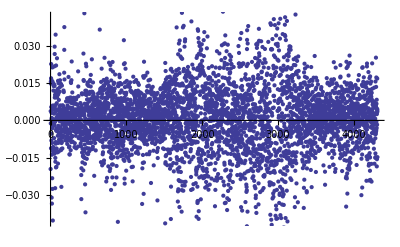

```mathematica
d=Differences[Log/@g];ListPlot[d]
```

```mathematica
n=Length[d];ds=Sort[d];F=Sort[Table[{ds[[i]],i/n},{i,1,n}]];
```

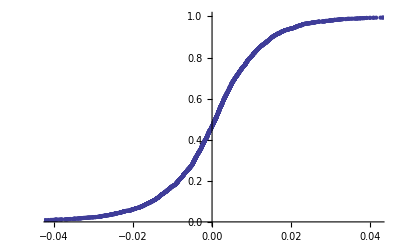

```mathematica
ListPlot[F]
```

```mathematica
model=b/Abs[x-u]^(1+a)
```

b Abs[-u+x]^(-1-a)

```mathematica
model=CDF[NormalDistribution[a,b],x]
```

1/2 (1+Erf[(-a+x)/(√2 b)])

```mathematica
fi=FindFit[F,model,{a,b,u},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→26.5444,b→89.7156,u→1.20858}

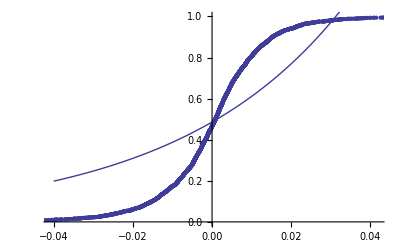

```mathematica
Show[ListPlot[{F}],Plot[model/.fi,{x,-0.04,0.04}]]
```

```mathematica
StandardDeviation[NormalDistribution[a,b]]/.fi
```

0.0108574

```mathematica
Sum[F[[i,1]]*(F[[i+1,2]]-F[[i,2]]),{i,1,n-1}]//N
```

0.00037817

```mathematica
StandardDeviation[ds]
```

0.0137907

```mathematica
2500*.01
```

25.

```mathematica
100
```

100

```mathematica
Sum[25^i Exp[-25]/i!,{i,0,20}]//N
```

0.185492

```mathematica
Sum[2500!/k!/(2500-k)!  .01^k (1-.01)^(2500-k),{k,0,20}]
```

0.184188